メゾンMを入れたポテンシャルのmoduli stabilization

```mathematica
ClearAll;
inittime=AbsoluteTime[];
zero[x_]=0;

W=w0+A Exp[-a T]+B Exp[-b T]+μ X M+α Λ^3*Exp[-c T]/M^(1/(n-1));
W̄=W/.{T->T̄,X->X̄,M->M̄};

K=-3Log[T+T̄]+Z X*X̄+ M*M̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, M]=D[W,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M]=D[K,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M̄]=D[K,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M M̄]=D[K,M,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T M̄]=D[K,T,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,X,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X M̄]=D[K,X,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M T̄]=D[K,M,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M X̄]=D[K,M,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};
DMW=Subscript[W, M]+Subscript[K, M]*W;
OverBar[DMW]=DMW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄],Subscript[K, T M̄]},{Subscript[K, X T̄],Subscript[K, X X̄],Subscript[K, X M̄]},{Subscript[K, M T̄],Subscript[K, M X̄],Subscript[K, M M̄]}};

Print["K_(I OverscriptBox[J, _])=",Kmat//MatrixForm];
Kinv=Inverse[Kmat];
Print["K^(I OverscriptBox[J, _])=",Kinv//MatrixForm];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, T M̄]=Kinv[[1,3]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];
Subscript[invK, X M̄]=Kinv[[2,3]];
Subscript[invK, M T̄]=Kinv[[3,1]];
Subscript[invK, M X̄]=Kinv[[3,2]];
Subscript[invK, M M̄]=Kinv[[3,3]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, T M̄]*(DTW)*(OverBar[DMW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])+Subscript[invK, X M̄]*(DXW)*(OverBar[DMW])+Subscript[invK, M T̄]*(DMW)*(OverBar[DTW])+Subscript[invK, M X̄]*(DMW)*(OverBar[DXW])+Subscript[invK, M M̄]*(DMW)*(OverBar[DMW])-3W*W̄);
(* Print["V=",vtemp]; *)

V=ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,M->ReM+I ImM,M̄->ReM-I ImM}];

Clear[w0];
w0=-Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]+δw0;

valδw0=0;
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

valn=2;
valΛ=10^(-3);
valC=1;
valλ=1;
valZ=1;

valμ=valλ*valΛ;
valα=valC*valΛ^(1/(valn-1));

(* mixing for moduli and mesons *)
valc=2Pi;

(* remove the dependence of the imaginary and insert parameters *)
V=Expand[V/.{ImM->0,ImX->0,ImT->0}/.{α->valα,n->valn,μ->valμ,Λ->valΛ,λ->valλ,Z->valZ}/.{a->vala,b->valb,A->valA,B->valB,c->valc,δw0->valδw0}/.Arg->zero];
Print["time: ",AbsoluteTime[]-inittime];
```

K_(I OverscriptBox[J, _])=(3/(T+T̄)^2 | 0 | 0
0 | Z | 0
0 | 0 | 1)

K^(I OverscriptBox[J, _])=(1/3 (T+T̄)^2 | 0 | 0
0 | 1/Z | 0
0 | 0 | 1)

time: 3.24168

General::munfl: Exp[-784.261]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

V_kl=1/((ReM^2)^(3/2))ⅇ^(ReM^2+ReX^2) (-5.12108×10^-179 ReM √(ReM^2)+ReM^5 (5.15412×10^-167-2.21875 √(ReM^2)) ReX+5.14231×10^12 ReM^6 √(ReM^2) ReX^2+ReM^2 (-3.15073×10^-170+5.12108×10^-179 ReX^2)+ReM^3 ReX (4.05248×10^-164-2.3958×10^7 √(ReM^2)+(5.15412×10^-167-2.21875 √(ReM^2)) ReX^2)+ReM^4 (5.12108×10^-179+5.14231×10^12 √(ReM^2)+2.05692×10^13 √(ReM^2) ReX^2+5.14231×10^12 √(ReM^2) ReX^4)+√(ReM^2) ReX (-5.15412×10^-167+ReM^2 (-5.15412×10^-167+5.14231×10^12 ReX)))

-Graphics3D-

FindMinimum::precw: 引数関数((ⅇ^(ReM^2+ReX^2) (-5.12108×10^-179 ReM √(ReM^2)+ReM^5 (5.15412×10^-167-2.21875 √(ReM^2)) ReX+5.14231×10^12 ReM^6 √(ReM^2) ReX^2+ReM^2 («1»)+ReM^3 ReX («1»)+ReM^4 (5.12108×10^-179+5.14231×10^12 √(ReM^2)+2.05692×10^13 √(ReM^2) ReX^2+5.14231×10^12 √(ReM^2) ReX^4)+√(ReM^2) ReX (-5.15412×10^-167+ReM^2 (-5.15412×10^-167+5.14231×10^12 ReX))))/((ReM^2)^(3/2)))の精度がWorkingPrecision (600.)より小さくなっています．

ReX→3.27×10^-60, ReM→3.27×10^-60

V_min=9.39521×10^-107

-Graphics3D-

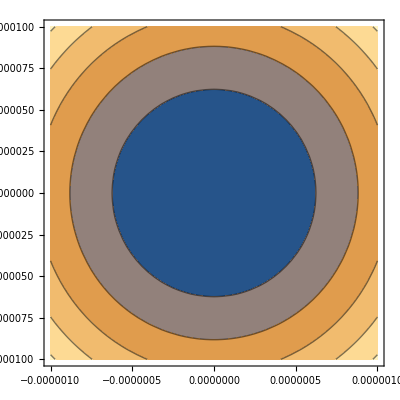

time: 0.4441012

```mathematica
inittime=AbsoluteTime[];
sc=10^(25);

Block[{$MaxPrecision=Infinity},
(* stabilized by KL moudli potential *)
Vkl=Simplify[Expand[V*sc/.{ReT->62.40947856364392}]];
Print["V_kl=",Vkl];

Print[
Plot3D[Vkl,{ReX,-1,1},{ReM,10^(-6),1},Axes->True,AxesLabel->{"X","M"}]
];

(* stabilized by remaing variables*)
sol=FindMinimum[Vkl,{ReX,10^(-4)},{ReM,10^(-4)},WorkingPrecision->600,AccuracyGoal->40];

Print[N[sol[[2]][[1]],3],", ",N[sol[[2]][[2]],3]];

rexmid=ReX/.sol[[2]];
remmid=ReM/.sol[[2]];

Print["V_min=",Vkl/.{ReX->rexmid,ReM->remmid}];

plran=10^(-6);

Print[
Plot3D[Vkl,{ReX,rexmid-plran,rexmid+plran},{ReM,remmid-plran,remmid+plran},Axes->True,AxesLabel->{"X","M"}]
];

Print[
ContourPlot[Vkl,{ReX,rexmid-plran,rexmid+plran},{ReM,remmid-plran,remmid+plran},Axes->True]
];

];


Print["time: ",AbsoluteTime[]-inittime];
```

```mathematica
(* stabilize taotally *)
Block[{$MaxExtraPrecision=Infinity},
sol=FindMinimum[V,{ReT,62},{ReX,10^(-4)},{ReM,10^(-4)},WorkingPrecision->600,AccuracyGoal->40];
Print["V_min=",N[sol[[1]],3]];
Print[N[sol[[2]],3]];
];

valT=ReT/.sol[[2]];
valM=ReM/.sol[[2]];
valX=ReX/.sol[[2]];

plran=10^(-3);

Print[
Plot3D[V*sc/.{ReT->valT},{ReX,valX-plran,valX+plran},{ReM,valM-plran,valM+plran},Axes->True,AxesLabel->{"X","M"}]
];

Print[
Plot3D[V*sc/.{ReX->valX},{ReT,valT-plran,valT+plran},{ReM,valM-plran,valM+plran},Axes->True,AxesLabel->{"T","M"}]
];

Print[
Plot3D[V*sc/.{ReM->valM},{ReT,valT-plran,valT+plran},{ReX,valX-plran,valX+plran},Axes->True,AxesLabel->{"T","X"}]
];
```

FindMinimum::precw: 引数関数((ⅇ^(ReM^2-4 π ReT+ReX^2))/(8000000000000000000000000 ReT^3)+(ⅇ^(ReM^2-4 π ReT+ReX^2))/(8000000000000000000000000 ReM^4 ReT^3)+(2.575×10^-13 ⅇ^(ReM^2-(200 π ReT)/99+ReX^2))/(ReM ReT^3)-(ⅇ^(ReM^2-(101 π ReT)/50+ReX^2))/(4000000000000 ReM ReT^3)+(4.95381×10^-17 ⅇ^(ReM^2-2 π ReT+ReX^2))/(ReM ReT^3)+(1.29908×10^-7 ⅇ^(ReM^2+ReX^2) ReM^2)/ReT^3+(0.132613 ⅇ^(ReM^2-(4 π ReT)/99+ReX^2) ReM^2)/ReT^3-(0.2575 ⅇ^(ReM^2-(199 π ReT)/4950+ReX^2) ReM^2)/ReT^3+(ⅇ^(ReM^2-(π ReT)/25+ReX^2) ReM^2)/(8 ReT^3)+(0.0000510242 ⅇ^(ReM^2-(2 π ReT)/99+ReX^2) ReM^2)/ReT^3+«50»)の精度がWorkingPrecision (600.)より小さくなっています．

V_min=-3.×10^-24

{ReT→62.4,ReX→5.77×10^-47,ReM→5.77×10^-47}

General::munfl: Exp[-784.261]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

-Graphics3D-

General::munfl: Exp[-784.248]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: -5.18608×10^-192 1.922527959057565143664793249788537319205639043496087579389221218765254494721374335220190895847785343922303497180495761295347554865927354383982098698770414052196850142767271208488032491110241594924148854193920404323528534238214646762483809569479990158527817744674729660947674446259900845087055687047221595805232521391123411602158316269935797728818468192110699572662321394635482150393755532675828415011988887821798717346581735889956179859338026149159080136709644450847021027352303508199139855949196043879567027676003346306143864609932012656615178012098331057798330791111464981779547997188538555779129×10^-139は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

-Graphics3D-

General::munfl: Exp[-784.248]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

-Graphics3D-

陳さんの修論の結果を再現

```mathematica
ClearAll;
inittime=AbsoluteTime[];
zero[x_]=0;

W=w0+μ X M+α Λ^3/M^(1/(n-1));
W̄=W/.{X->X̄,M->M̄};

Print["W=",W];

K=Z X X̄+M M̄-15;

Print["K=",K];

Subscript[W, M]=D[W,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M]=D[K,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M̄]=D[K,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M M̄]=D[K,M,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X M̄]=D[K,X,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M X̄]=D[K,M,X̄]/.{OverBar'->zero,OverBar''->zero};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{X->X̄,X̄->X,M->M̄,M̄->M};
DMW=Subscript[W, M]+Subscript[K, M]*W;
OverBar[DMW]=DMW/.{X->X̄,X̄->X,M->M̄,M̄->M};

Kmat={{Subscript[K, X X̄],Subscript[K, M X̄]},{Subscript[K, X M̄],Subscript[K, M M̄]}};

Print["K_(I OverscriptBox[J, _])=",Kmat//MatrixForm];
Kinv=Inverse[Kmat];
Print["K^(I OverscriptBox[J, _])=",Kinv//MatrixForm];
Subscript[invK, X X̄]=Kinv[[1,1]];
Subscript[invK, X M̄]=Kinv[[1,2]];
Subscript[invK, M X̄]=Kinv[[2,1]];
Subscript[invK, M M̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])+Subscript[invK, X M̄]*(DXW)*(OverBar[DMW])+Subscript[invK, M X̄]*(DMW)*(OverBar[DXW])+Subscript[invK, M M̄]*(DMW)*(OverBar[DMW])-3W*W̄);
Print["V=",vtemp];

V=ComplexExpand[vtemp/.{X->ReX+I ImX,X̄->ReX-I ImX,M->ReM+I ImM,M̄->ReM-I ImM}];
(* Print["V=",V]; *)

Print["time: ",AbsoluteTime[]-inittime];
```

W=w0+M^(-1/(-1+n)) α Λ^3+M X μ

K=-15+M M̄+X Z X̄

K_(I OverscriptBox[J, _])=(Z | 0
0 | 1)

K^(I OverscriptBox[J, _])=(1/Z | 0
0 | 1)

V=ⅇ^(-15+M M̄+X Z X̄) (-3 (w0+M^(-1/(-1+n)) α Λ^3+M X μ) (w0+α Λ^3 (M̄)^(-1/(-1+n))+μ M̄ X̄)+(-(M^(-1-1/(-1+n)) α Λ^3)/(-1+n)+X μ+(w0+M^(-1/(-1+n)) α Λ^3+M X μ) M̄) (-(α Λ^3 (M̄)^(-1-1/(-1+n)))/(-1+n)+μ X̄+M (w0+α Λ^3 (M̄)^(-1/(-1+n))+μ M̄ X̄))+((M μ+Z (w0+M^(-1/(-1+n)) α Λ^3+M X μ) X̄) (μ M̄+X Z (w0+α Λ^3 (M̄)^(-1/(-1+n))+μ M̄ X̄)))/Z)

time: 0.0468153

5.76×10^-19

ReX→4.94×10^-6, ReM→0.00112

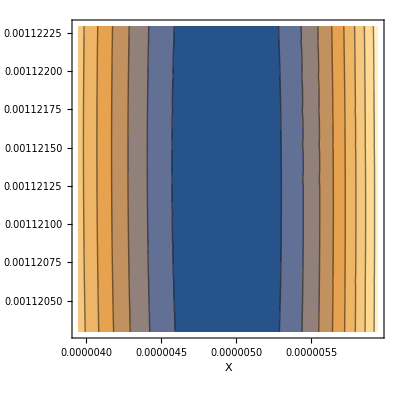

-Graphics3D-

time: 19.380845

```mathematica
inittime=AbsoluteTime[];
valw0=10^(-16);
valn=2;
valΛ=10^(-3);
valC=1;
valλ=1;
valZ=1;

valμ=valλ*valΛ;
valα=valC*valΛ^(1/(valn-1));

(* Print["V=",V/.{ImM->0,ImX->0}/.Arg->zero/.{α->valα,n->valn,μ->valμ,Λ->valΛ,λ->valλ,Z->valZ,w0->valw0}]; *)

sol=FindMinimum[(ReX^4+V)/.{ImM->0,ImX->0}/.Arg->zero/.{α->valα,n->valn,μ->valμ,Λ->valΛ,λ->valλ,Z->valZ,w0->valw0},{ReX,10^(-4)},{ReM,10^(-4)},WorkingPrecision->600,AccuracyGoal->40,PrecisionGoal->Infinity,MaxIterations->300,Method->"InteriorPoint"];

Print[N[sol[[1]],3]];
Print[N[sol[[2]][[1]],3],", ",N[sol[[2]][[2]],3]];

rexmid=ReX/.sol[[2]];
remmid=ReM/.sol[[2]];

plran=10^(-6);

Print[
ContourPlot[(ReX^4+V)*10^(25)/.{ImM->0,ImX->0}/.Arg->zero/.{α->valα,n->valn,μ->valμ,Λ->valΛ,λ->valλ,Z->valZ,w0->valw0},{ReX,rexmid-plran,rexmid+plran},{ReM,remmid-plran,remmid+plran},Axes->True,AxesLabel->{"X","M"},PlotPoints->10,WorkingPrecision->500]
];

Print[
Plot3D[(ReX^4+V)*10^(25)/.{ImM->0,ImX->0}/.Arg->zero/.{α->valα,n->valn,μ->valμ,Λ->valΛ,λ->valλ,Z->valZ,w0->valw0},{ReX,rexmid-plran,rexmid+plran},{ReM,remmid-plran,remmid+plran},Axes->True,AxesLabel->{"X","M"},PlotPoints->10,WorkingPrecision->500]
];

Print["time: ",AbsoluteTime[]-inittime];
```

KL problemのチェック

```mathematica
ClearAll;

zero[x_]=0;

W=w0+A Exp[-a T]+B Exp[-b T];
W̄=W/.{T->T̄};
K=-3Log[T+T̄];

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T};

vtemp=Exp[K]*((Subscript[K, T T̄])^(-1)*(DTW)*(OverBar[DTW])-3W*W̄);
Print["V=",vtemp];

V=FullSimplify@ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT}];
Print["V=",V];V=FullSimplify[V/.{ImT->0,w0->-Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]+δw0}];
Print["V=",V];
```

V=(-3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0) (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0)+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-b B ⅇ^(-b T)-(3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0))/(T+T̄)) (-a A ⅇ^(-a T̄)-b B ⅇ^(-b T̄)-(3 (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0))/(T+T̄)))/(T+T̄)^3

V=(ⅇ^(-2 (a+b) ReT) (a A^2 ⅇ^(2 b ReT) (3+a ReT)+b B^2 ⅇ^(2 a ReT) (3+b ReT)+ⅇ^((a+b) ReT) (3 a A ⅇ^(b ReT) w0 Cos[a ImT]+A B (3 (a+b)+2 a b ReT) Cos[(a-b) ImT]+3 b B ⅇ^(a ReT) w0 Cos[b ImT])))/(6 ReT^2)

V=(ⅇ^(-2 (a+b) ReT) (b B ⅇ^(a ReT)+a A ⅇ^(b ReT)) (B ⅇ^(a ReT) (3+b ReT)+ⅇ^(b ReT) (3 A+a A ReT+3 ⅇ^(a ReT) δw0)-3 ⅇ^((a+b) ReT) Abs[Abs[(a A)/(b B)]^(-b/(a-b)) (B+A Abs[(b B)/(a A)])]))/(6 ReT^2)

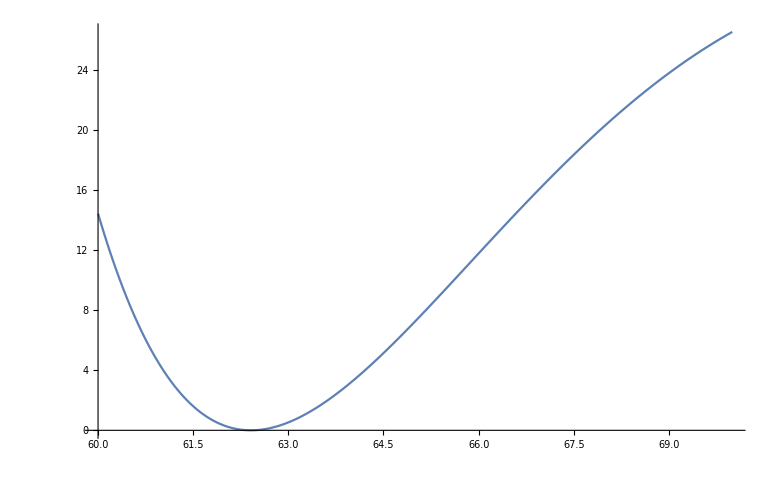

<T>=62.4095

W=-2.22045×10^-16

K=-14.4806

```mathematica
valδw0=0;
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

init=60;

Print[
Plot[V*10^(15)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,init,init+10},WorkingPrecision->100,PlotPoints->200]
];

sol=FindMinimum[V*10^(10)/.w0->-Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,62,70},PrecisionGoal->Infinity];
valT=ReT/.sol[[2]];

Print["<T>=",valT];

Print["W=",W/.w0->-Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.T->valT];
Print["K=",K/.w0->-Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT}];
```

KKLT

```mathematica
ClearAll;

zero[x_]=0;

W=w0+A Exp[-a T];
W̄=W/.{T->T̄};
K=-3Log[T+T̄];

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T};

vtemp=Exp[K]*((Subscript[K, T T̄])^(-1)*(DTW)*(OverBar[DTW])-3W*W̄);
Print["V=",vtemp];

V=FullSimplify@ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT}];
Print["V=",V];
```

V=(-3 (A ⅇ^(-a T)+w0) (A ⅇ^(-a T̄)+w0)+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-(3 (A ⅇ^(-a T)+w0))/(T+T̄)) (-a A ⅇ^(-a T̄)-(3 (A ⅇ^(-a T̄)+w0))/(T+T̄)))/(T+T̄)^3

V=(a A ⅇ^(-2 a ReT) (A (3+a ReT)+3 ⅇ^(a ReT) w0 Cos[a ImT]))/(6 ReT^2)

```mathematica
V=FullSimplify[V/.{ImT->Pi/a,w0->Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]}];
Print["V=",V];
```

V=(a A ⅇ^(-2 a ReT) (A (3+a ReT)-3 ⅇ^(a ReT) Abs[A Abs[(a A)/(b B)]^(a/(-a+b))+B Abs[(a A)/(b B)]^(b/(-a+b))]))/(6 ReT^2)

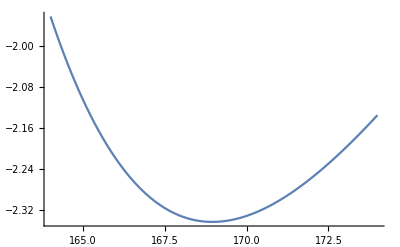

```mathematica
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

init=164;
Plot[V*10^(15)/.{a->vala,b->valb,A->valA,B->valB},{ReT,init,init+10},WorkingPrecision->100,PlotPoints->200]
```